# Model predictions for Fig . 5

#### The following models are included: - simple model - model with lag - model with multiple alleles - model with filamentation

## Setting up and helper functions

```mathematica
colors={Darker[Green],Darker[Red],Blue,Purple,Darker[Magenta],Pink}
```

{RGBColor[0, Rational[2, 3], 0],RGBColor[Rational[2, 3], 0, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],RGBColor[Rational[2, 3], 0, Rational[2, 3]],RGBColor[1, 0.5, 0.5]}

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListDensityPlot,ListLinePlot,Histogram,BarChart,Graphics},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];
```

```mathematica
Clear[RegrowthProbs]
RegrowthProbs[names_]:=Module[{gr,pexp,pth,simdist,tmp2},
Do[
simdist=Table[Import["models\\"<>names[[j]]<>"\\distribution_data_"<>ToString[nn]<>".dat","Table"],{nn,{2}}];
tmp2=Flatten[simdist,1];
pth=1.Length[Select[tmp2,NumberQ[#1⟦2⟧]&]]/Length[tmp2];
Print["mean P_regrowth= ",pth," conf. intervals: ",{1.(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],1.(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]}/.{z->1,n->Length[tmp2],m->Length[Select[tmp2,(NumberQ[#[[2]]]&)]]}];
,{j,Length[names]}];
]
Clear[PlotWTandMutants]
PlotWTandMutants[name_,totcols_,cols_,color_,output_]:=Module[{nns=ReadList[name,Table[Number,{totcols}]],tmax,nmax,pl1,pl2,pl},
tmax=Max[nns[[All,1]]];nmax=Max[nns[[All,cols[[1]]]]];
pl1=ListDensityPlot[Transpose[BinCounts[{#[[1]],Log[1.#[[2]]]}&/@nns[[All,{1,cols[[1]]}]],{0,tmax,0.1},{0,Log[nmax],0.2}]],ColorFunction->(RGBColor[0,0,0,#]&),PlotRange->All,InterpolationOrder->0,DataRange->{{0,tmax},{0,Log[nmax]}}];
pl2=ListDensityPlot[Transpose[BinCounts[{#[[1]],Log[1.#[[2]]]}&/@nns[[All,{1,cols[[2]]}]],{0,tmax,0.1},{0,Log[nmax],0.5}]],ColorFunction->(Opacity[#^0.5,color]&),PlotRange->All,InterpolationOrder->0,DataRange->{{0,tmax},{0,Log[nmax]}}];
pl=Show[pl1,pl2,AspectRatio->1,ImageSize->300,FrameTicks->{{{{Log[1],"1"},{Log[10^2],"10^2"},{Log[10^4],"10^4"},{Log[10^6],"10^6"},{Log[10^8],"10^8"},{Log[10^10],"10^10"}},None},{Automatic,Automatic}},BaseStyle->FontSize->24,FrameLabel->{"t [h]","N"}];
Export[output,pl,"PNG"];
Print[pl];
]
```

```mathematica
mutrate="1.5e-9";  (* we shall use the same value for all models *)
mu=Interpreter["Number"][mutrate]
```

1.5×10^-9

## Exponential growth

### Parameters common to all models :

```mathematica
ainjs=100;
tends=5;
tmax=100;
noreps="300";
tmax=35;
odinit=5 10^-5.;
odregrowth=0.05;
dilf=0.75;
vol=30;
```

## Simple model:

```mathematica
strains=1;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* mutant strains before and after the antibiotic *)
mt={2{1},2{1}};

Export[NotebookDirectory[]<>"\\models\\prediction_simple_exp\\input_params_"<>ToString[nn]<>".dat",Join[{"GENERIC",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_simple_exp"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_simple_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_1 30 0.00005 100 5 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
PlotWTandMutants["models\\prediction_simple_exp\\n_data_1.dat",6,{2,3},colors[[1]],"figures\\prediction_simple_exp.png"]
```

-Graphics-

### treatment at t_end for another 30 h:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_simple_exp"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_simple_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_2 30 0.00005 5 35 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
RegrowthProbs[{"prediction_simple_exp"}]
```

mean P_regrowth= 0.497667 conf. intervals: {0.48854,0.506795}

## Model with lag

```mathematica
lagrate="0.04" ; 
intgrfraction=0.0; (* much less than in reality *)

strains=1;alleles=1;
mutprobs={1,1};
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* intermediate strains before and after the antibiotics*)
it={2{1},intgrfraction 2{1}};
(* mutant strains before and after the antibiotic *)
mt={2{1},2{1}};

Export[NotebookDirectory[]<>"\\models\\prediction_lag_exp\\input_params_"<>ToString[nn]<>".dat",Join[{"GENERIC",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs,{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_lag_exp"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_lag_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 1 14 data_1 30 0.00005 100 5 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat  0.1  0.04

0

```mathematica
PlotWTandMutants["models\\prediction_lag_exp\\n_data_1.dat",5,{2,4},colors[[2]],"figures\\prediction_lag_exp.png"]
```

-Graphics-

### treatment at t_end for another 30 h:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_lag_exp"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_lag_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 1 14 data_2 30 0.00005 5 35 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat  0.1  0.04

0

```mathematica
RegrowthProbs[{"prediction_lag_exp"}]
```

mean P_regrowth= 0.084 conf. intervals: {0.0790732,0.0892041}

## Model with multiple alleles

```mathematica
tmp=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]];
allrates={"rpoB "<>#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&];
LBrates=allrates[[All,2]];
RIFrates=allrates[[All,3]];

strains=1;
alleles=Length[LBrates];

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
mt=2mt/Max[mt]; (* normalize so that no growth rate is higher than WT *)
Export[NotebookDirectory[]<>"\\models\\prediction_mult_exp\\input_params_"<>ToString[nn]<>".dat",Join[{"GENERIC",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_mult_exp"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_mult_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_1 30 0.00005 100 5 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
PlotWTandMutants["models\\prediction_mult_exp\\n_data_1.dat",6,{2,3},colors[[3]],"figures\\prediction_mult_exp.png"]
```

-Graphics-

### treatment at t_end for another 30 h:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_mult_exp"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_mult_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_2 30 0.00005 5 35 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
RegrowthProbs[{"prediction_mult_exp"}]
```

mean P_regrowth= 0.313667 conf. intervals: {0.305259,0.322199}

## Filamentation

```mathematica
strains=1;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* mutant strains before and after the antibiotic *)
mt={2{1},2{1}};

Export[NotebookDirectory[]<>"\\models\\prediction_filam_exp\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_filam_exp"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_filam_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_1 30 0.00005 100 5 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
PlotWTandMutants["models\\prediction_filam_exp\\n_data_1.dat",6,{2,3},colors[[4]],"figures\\prediction_filam_exp.png"]
```

-Graphics-

### treatment at t_end for another 30 h:

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_filam_exp"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_filam_exp

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_2 30 0.00005 5 35 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
RegrowthProbs[{"prediction_filam_exp"}]
```

mean P_regrowth= 0.37 conf. intervals: {0.36123,0.378857}

## Steady - state growth

### Parameters common to all models :

```mathematica
ainjs=100;
tends=50;
tmax=100;
noreps="300";
tmax=35;
odinit= 10^-5.;
odregrowth=0.05;
dilf=0.75;
vol=6;
```

## Simple model:

```mathematica
strains=1;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* mutant strains before and after the antibiotic *)
mt={2{1},2{1}};

Export[NotebookDirectory[]<>"\\models\\prediction_simple_ss\\input_params_"<>ToString[nn]<>".dat",Join[{"GENERIC",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_simple_ss"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_simple_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_1 6 0.00001 100 50 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
PlotWTandMutants["models\\prediction_simple_ss\\n_data_1.dat",6,{2,3},colors[[1]],"figures\\prediction_simple_ss.png"]
```

-Graphics-

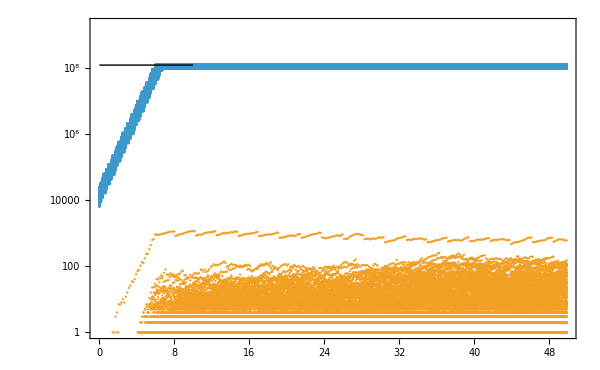

```mathematica
kk=1;
nns=ReadList["models\\prediction_simple_ss\\n_data_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[;;;;10,{1,2}]],nns[[;;;;10,{1,3}]]},ImageSize->600,PlotRange->{1,2 10^9},Epilog->Line[{{0,Log[vol 2 10^7]},{10,Log[vol 2 10^7]}}]]
```

### treatment at t_end, then + 30 h run :

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_simple_ss"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_simple_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_2 6 0.00001 50 80 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
RegrowthProbs[{"prediction_simple_ss"}]
```

mean P_regrowth= 0.504333 conf. intervals: {0.495205,0.513459}

## Model with lag

```mathematica
lagrate="0.04" ; 
intgrfraction=0.0; 

strains=1;alleles=1;
mutprobs={1,1};
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* intermediate strains before and after the antibiotics*)
it={2{1},intgrfraction 2{1}};
(* mutant strains before and after the antibiotic *)
mt={2{1},2{1}};

Export[NotebookDirectory[]<>"\\models\\prediction_lag_ss\\input_params_"<>ToString[nn]<>".dat",Join[{"GENERIC",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],mutprobs,{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_lag_ss"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_lag_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 1 14 data_1 6 0.00001 100 50 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat  0.1  0.04

0

```mathematica
PlotWTandMutants["models\\prediction_lag_ss\\n_data_1.dat",5,{2,4},colors[[2]],"figures\\prediction_lag_ss.png"]
```

-Graphics-

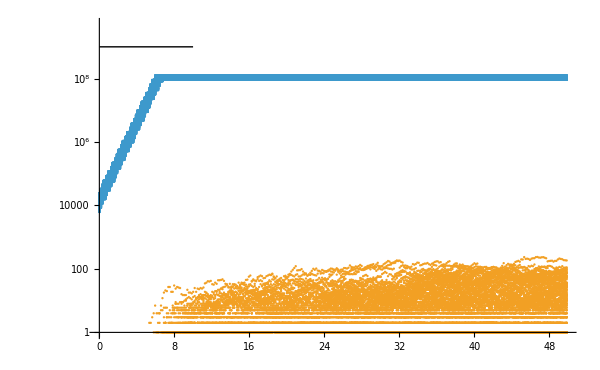

```mathematica
kk=1;
nns=ReadList["models\\prediction_lag_ss\\n_data_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[;;;;10,{1,2}]],nns[[;;;;10,{1,4}]]},ImageSize->600,PlotRange->{1,5 10^9},Epilog->Line[{{0,Log[10^9]},{10,Log[10^9]}}]]
```

### treatment at t_end, then + 30 h run :

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_lag_ss"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_lag_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 1 14 data_2 6 0.00001 50 80 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat  0.1  0.04

0

```mathematica
RegrowthProbs[{"prediction_lag_ss"}]
```

mean P_regrowth= 0.305667 conf. intervals: {0.297322,0.314141}

## Model with multiple alleles

```mathematica
tmp=Import["RifR_mutants_turb_growth_summary_automated_grrates_made_to_work.xlsx","XLSX"][[1]];
allrates={"rpoB "<>#[[1,3]],Mean[#[[All,5]]],Mean[#[[All,7]]]}&/@Gather[tmp[[2;;]],(#1[[3]]==#2[[3]])&];
LBrates=allrates[[All,2]];
RIFrates=allrates[[All,3]];

strains=1;
alleles=Length[LBrates];

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* mutant strains before and after the antibiotic *)
mt={Flatten[Table[Table[LBrates[[i]],{strains}],{i,alleles}]],Flatten[Table[Table[RIFrates[[i]],{strains}],{i,alleles}]]};
mt=2mt/Max[mt]; (* normalize so that no growth rate is higher than WT *)

Export[NotebookDirectory[]<>"\\models\\prediction_mult_ss\\input_params_"<>ToString[nn]<>".dat",Join[{"GENERIC",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_mult_ss"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_mult_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 14 data_1 6 0.00001 100 50 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat  0.1  0.04

0

```mathematica
PlotWTandMutants["models\\prediction_mult_ss\\n_data_1.dat",6,{2,3},colors[[3]],"figures\\prediction_mult_ss.png"]
```

-Graphics-

```mathematica
kk=1;
nns=ReadList["models\\prediction_mult_ss\\n_data_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[;;;;10,{1,2}]],nns[[;;;;10,{1,3}]]},ImageSize->600,PlotRange->{1,2 10^9},Epilog->Line[{{0,Log[10^9]},{10,Log[10^9]}}]]
```

-Graphics-

### treatment at t_end, then + 30 h run :

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_mult_ss"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat")," 0.1 ",lagrate},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_mult_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 14 data_2 6 0.00001 50 80 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat  0.1  0.04

0

```mathematica
RegrowthProbs[{"prediction_mult_ss"}]
```

mean P_regrowth= 0.171333 conf. intervals: {0.164564,0.178322}

## Filamentation

```mathematica
strains=1;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={2{1},{0}};
(* mutant strains before and after the antibiotic *)
mt={2{1},2{1}};

Export[NotebookDirectory[]<>"\\models\\prediction_filam_ss\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","2.0",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,1}]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_filam_ss"]
args=Table[
{"data_"<>ToString[1],ToString[vol],ToString[odinit],ToString[ainjs],ToString[tends],ToString[tmax],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_filam_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_1 6 0.00001 100 50 35 0.05 300 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
PlotWTandMutants["models\\prediction_filam_ss\\n_data_1.dat",6,{2,3},colors[[4]],"figures\\prediction_filam_ss.png"]
```

-Graphics-

```mathematica
kk=1;
nns=ReadList["models\\prediction_filam_ss\\n_data_"<>ToString[kk]<>".dat",{Number,Number,Number,Number,Number,Number}];
ListLogPlot[{nns[[;;;;10,{1,2}]],nns[[;;;;10,{1,3}]]},ImageSize->600,PlotRange->{1,2 10^9},Epilog->Line[{{0,Log[10^9]},{10,Log[10^9]}}]]
```

-Graphics-

### treatment at t_end, then + 30 h run :

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\prediction_filam_ss"]
args=Table[
{"data_"<>ToString[2],ToString[vol],ToString[odinit],ToString[tends],ToString[tends+30],ToString[tmax],ToString[odregrowth],"3000",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[1]<>".dat"),"0.1"},{nn,1}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\prediction_filam_ss

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 1 13 data_2 6 0.00001 50 80 35 0.05 3000 1.5000000000000002e-9 1.5000000000000002e-9 0.75 input_params_1.dat 0.1

0

```mathematica
RegrowthProbs[{"prediction_filam_ss"}]
```

mean P_regrowth= 0.413 conf. intervals: {0.404041,0.422017}

## Summary

```mathematica
Clear[MakeBar2,MakeBarFromNM,RegrowthProbPlot]
MakeBar2[x_,y1_,y2_]:={AbsolutePointSize[10],Point[{x,(y1+y2)/2}],AbsoluteThickness[2],Line[{{x-0.25,y1},{x+0.25,y1}}],Line[{{x-0.25,y2},{x+0.25,y2}}],AbsoluteThickness[1],Line[{{x-0.15,y1},{x+0.15,y1}}],Line[{{x-0.15,y2},{x+0.15,y2}}],Line[{{x,y1},{x,y2}}]};
MakeBarFromNM[x_,n_,m_]:=MakeBar2[x,(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]]/.z->1 (* Wilson score interval https://en.wikipedia.org/wiki/Binomial_proportion_confidence_interval *)
RegrowthProbPlot[names_,name_]:=Module[{gr,pexp,pth,simdist,tmp={},tmp2},
Do[
simdist=Table[Import["models\\"<>names[[j]]<>"\\distribution_data_"<>ToString[nn]<>".dat","Table"],{nn,{2}}];
tmp2=Flatten[simdist,1];
pth=Length[Select[tmp2,NumberQ[#1⟦2⟧]&]]/Length[tmp2];
AppendTo[tmp,tmp2];
,{j,Length[names]}];

gr=Graphics[Flatten[{Table[{colors[[i]],MakeBarFromNM[0.7+0.8i,Length[tmp[[i]]],Length[Select[tmp[[i]],(NumberQ[#[[2]]]&)]]]},{i,Length[tmp]}]}],(*Epilog->{Text["g_s",{0.7,0}],Text["g_r",{1.5,0}]},*)Axes->{None,Automatic},PlotRange->{{0,1.2+0.8Length[tmp]},{0,0.6}},Axes->True,Frame->False,AxesLabel->{None,"P_regrowth"},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AspectRatio->1.3,ImageSize->200];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];]
```

```mathematica
RegrowthProbPlot[{"prediction_simple_ss","prediction_lag_ss","prediction_mult_ss","prediction_filam_ss"},"predictions_Pregrowth_ss.png"]
```

-Graphics-

```mathematica
RegrowthProbPlot[{"prediction_simple_exp","prediction_lag_exp","prediction_mult_exp","prediction_filam_exp"},"predictions_Pregrowth_exp.png"]
```

-Graphics-